# Équation d'onde classique

## Corde tendue libre aux points x=0 et x=L

## Exemple 1

## Caracteristique de la corde

```mathematica
ClearAll["Global`*"]
```

Longueur de la corde (m)

```mathematica
L:=1
```

Masse de la corde (Kg)

```mathematica
m:=0.1
```

Tension dans la corde (N)

```mathematica
T:=10
```

Densité linéaire uniforme (Kgm^-1)

```mathematica
μ=m/L
```

0.1

Vitesse de phase (ms^-1)

```mathematica
v=√(T/μ)
```

10.

## Les conditions aux frontières

```mathematica
ψ[0,t_]:=0;
```

```mathematica
ψ[L,t_]:=0;
```

## Les conditions initiales

La forme initiale :

```mathematica
ψ[x_,0]:=x;
```

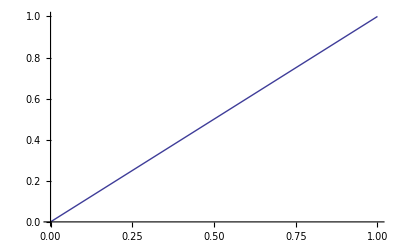

```mathematica
Plot[ψ[x,0],{x,0,L}]
```

La vitesse initiale :

```mathematica
ψ'[x_,0]:=0
```

## Solution

Les valeures propres de l'équation de Helmhotz pour X[x]

```mathematica
Subscript[k, n_]:=(n π)/L
```

Les fonctions propres de l'équation de Helmhotz pour X[x]

```mathematica
Subscript[X, n_][x_]:=Sin[Subscript[k, n]  x+π/2]
```

Les valeures propres  de l'équation de Helmhotz pour T[t]

```mathematica
Subscript[ω, n_]=Subscript[k, n] v
```

31.4159 n

Les coéficients A_n et B_n

```mathematica
Subscript[A, n_]=2/L ∫_0^L ψ[x,0]Sin[Subscript[k, n] x]ⅆx
```

(2 (-n π Cos[n π]+Sin[n π]))/(n^2 π^2)

```mathematica
Subscript[B, n_]=2/(Subscript[ω, n] L) ∫_0^L ψ'[x,0]Sin[Subscript[k, n] x]ⅆx
```

0.

Les fonctions propres  de l'équation de Helmhotz pour T[t]

```mathematica
Subscript[T, n_][t_]:=Subscript[A, n] Cos[Subscript[ω, n] t]+Subscript[B, n] Sin[Subscript[ω, n] t]
```

Les composantes de la fonction d'onde

```mathematica
Subscript[ψ, n_][x_,t_]=Subscript[X, n][x]Subscript[T, n][t]
```

Cos[n π x] (0.+(2 Cos[31.4159 n t] (-n π Cos[n π]+Sin[n π]))/(n^2 π^2))

Longueur d' onde des composantes de la fonction d'onde

```mathematica
Subscript[λ, n_]=(2π)/Subscript[k, n]
```

2/n

Fréquence des composantes de la fonction d'onde

```mathematica
Subscript[ν, n_]=v/Subscript[λ, n]
```

5. n

Fonction d' onde

```mathematica
ψ[x_,t_]=∑_(n=1)^6 Subscript[ψ, n][x,t]
```

(0.+(2 Cos[31.4159 t])/π) Cos[π x]+(0.-Cos[62.8319 t]/π) Cos[2 π x]+(0.+(2 Cos[94.2478 t])/(3 π)) Cos[3 π x]+(0.-Cos[125.664 t]/(2 π)) Cos[4 π x]+(0.+(2 Cos[157.08 t])/(5 π)) Cos[5 π x]+(0.-Cos[188.496 t]/(3 π)) Cos[6 π x]

## Tableau

```mathematica
expr1:=n
```

```mathematica
expr2:=Subscript[ψ, n][x,0]
```

```mathematica
expr3:=Plot[Subscript[ψ, n][x,0],{x,0,L},Frame->True]
```

```mathematica
expr4:=Subscript[λ, n]
```

```mathematica
table:=Table[{expr1,expr2,expr3,expr4},{n,1,6}]
```

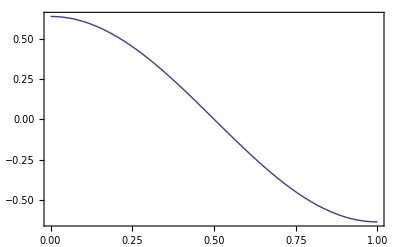
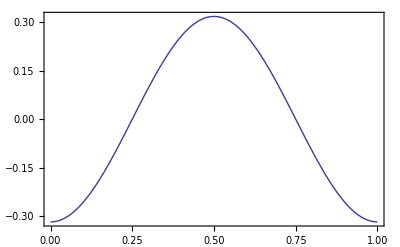
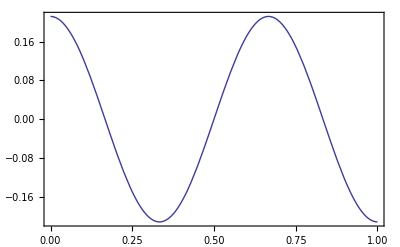
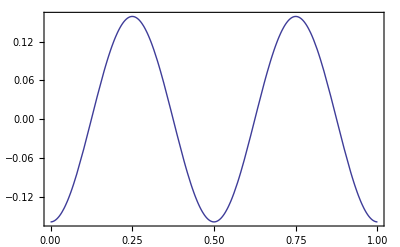
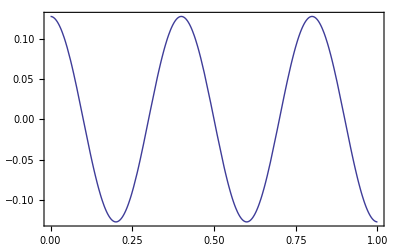
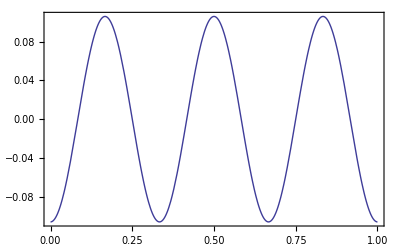
1 | 0.63662 cos(π x) | -Graphics- | 2
2 | -0.31831 cos(2 π x) | -Graphics- | 1
3 | 0.212207 cos(3 π x) | -Graphics- | 2/3
4 | -0.159155 cos(4 π x) | -Graphics- | 1/2
5 | 0.127324 cos(5 π x) | -Graphics- | 2/5
6 | -0.106103 cos(6 π x) | -Graphics- | 1/3

```mathematica
Grid[table,Frame->All]//TraditionalForm
```

## Visualisation

### Représentation des modes normeaux

```mathematica
Manipulate[Plot[Subscript[ψ, Mode][x,t],{x,0,L},PlotRange->{-N[Subscript[A, Mode]+Subscript[B, Mode]],N[Subscript[A, Mode]+Subscript[B, Mode]]},Frame->True],{Mode,{1,2,3,4,5,6,7,8,9,10,11,12}},{t,0,(2L)/v}]
```

### Représentation de superpositions des modes normeaux

```mathematica
Manipulate[Plot[ψ[x,t],{x,0,L},PlotRange->{-1,1},Frame->True],{t,0,(2L)/v}]
```